```mathematica
Γ=0.05;
ϵ=0;
ω=3;
Subscript[ω, 0]=3;
a=Subscript[Δ, 0]/ω;
L1=(n-m)*Subscript[ω, 0];
Subscript[D, nm]=Exp[-g^2/2]∑_(o=0)^Min[n,m] (((-1)^o*√(n!*m!)*(g)^(n+m-2*o))/((n-o)!*(m-o)!o!));
f[x_]:=Γ^2/1∑_(h=-2)^2 1/((x-ϵ-h*ω)^2+Γ^2)*(BesselJ[Abs[h],a])^2(Exp[β(x+a1)](1+Exp[β(x+a1)])^-2+Exp[β(x-a1)](1+Exp[β(x-a1)])^-2)
P[x_]:=1/2 Γ^2∑_(h=-2)^2 ∑_(n=0)^2 ∑_(m=0)^1 (Subscript[D, nm])^2(1/((x-ϵ-h*ω-L1)^2+Γ^2))(1/(Exp[β(m*Subscript[ω, 0])]+Exp[β((m-1)*Subscript[ω, 0])])+1/(Exp[β(n*Subscript[ω, 0])]+Exp[β((n-1)*Subscript[ω, 0])]+Exp[β((n-2)*Subscript[ω, 0])]))*(BesselJ[Abs[h],a])^2(Exp[β(x+a1)](1+Exp[β(x+a1)])^-2+Exp[β(x-a1)](1+Exp[β(x-a1)])^-2)

Subscript[X, I]=-10;
Subscript[X, F]=10;
l=1000;
H=(Subscript[X, F]-Subscript[X, I])/l;
x=Subscript[X, I];
A=∑_(k=1)^l f[x+k*H];
B=∑_(k=1)^l P[x+k*H];
Fi=(H/2*(f[-10]+f[10]+2*A));
Gi=(H/2*(P[-10]+P[10]+2*B));
```

```mathematica
β=3.5;
Subscript[Δ, 0]=0;
g=1.5;
LL=Gi;
```

```mathematica
β=3.5;
Subscript[Δ, 0]=5;
LL1=Fi;
```

```mathematica
β=3.5;
Subscript[Δ, 0]=5;
g=1.5;
LL2=Gi;
```

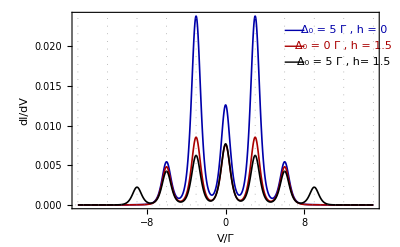

```mathematica
Plot[{LL1,LL,LL2},{a1,-15,15},GridLines->{{-15,-12,-9,-6,-3,3,6,9,12,15},{0}},GridLinesStyle->Directive[Gray,Dotted],ImagePadding->70,Frame-> True,FrameLabel->{Style["V/Γ",Small,Bold,Black],Style[" dI/dV" ,Small,Bold,Black]},PlotStyle->{{Directive[Darker[Blue]],Thickness[0.003]},{Directive[Darker[Red]],Thickness[0.003]},{Directive[Darker[Black]],Thickness[0.003]}}, Epilog->{Darker[Blue],Line[{{6,.022},{8,.022}}],Text[" Δ_0 = 5 Γ , h = 0 ",{12,.022}],Darker[Red],Line[{{6,.02},{8,.02}}],Text[" Δ_0 = 0 Γ , h = 1.5 ",{12,.02}],
Darker[Black],Line[{{6,.018},{8,.018}}],Text[" Δ_0 = 5 Γ , h= 1.5 ",{12,.018}]},ImageSize->Scaled[0.75],PlotRange->Full]
```

```mathematica
Γ=0.05;
ϵ=0;
μ=0;
ω=3;
a=Subscript[Δ, 0]/ω;
β=3.5;

f[x_]:=Γ^2/1∑_(h=-2)^2 1/((x-ϵ-h*ω)^2+Γ^2)*(BesselJ[Abs[h],a])^2(-(1+Exp[β(x+μ+a1)])^-1+(1+Exp[β(x+μ-a1)])^-1)
P[x_]:=Γ^2/1∑_(h=-2)^2 1/((x-ϵ-h*ω)^2+Γ^2)*(BesselJ[Abs[h],a])^2(Exp[β(x+μ+a1)](1+Exp[β(x+μ+a1)])^-2+Exp[β(x+μ-a1)](1+Exp[β(x+μ-a1)])^-2)
Subscript[X, I]=-30;
Subscript[X, F]=30;
l=1000;
H=(Subscript[X, F]-Subscript[X, I])/l;
x=Subscript[X, I];
A=∑_(k=1)^l f[x+k*H];
B=∑_(k=1)^l P[x+k*H];
Fi=(H/2*(f[-30]+f[30]+2*A));
Gi=(H/2*(P[-30]+P[30]+2*B));
```

```mathematica
Subscript[Δ, 0]=0;
LL=Fi;
```

```mathematica
Subscript[Δ, 0]=5;
LL1=Fi;
```

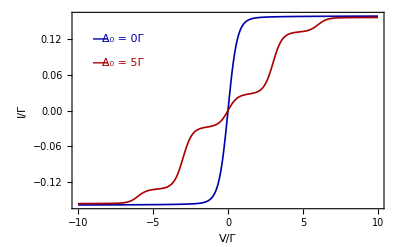

```mathematica
plot1=Plot[{LL,LL1},{a1,-10,10},ImagePadding->70,Frame->{True,True,True,False},FrameStyle->{Automatic,Black,Automatic,Automatic},ImageSize->Scaled[0.75],FrameLabel->{{Style["I/Γ ",Small,Bold,Black],None},{Style["V/Γ " ,Small,Bold,Black],None}},PlotStyle->{{Directive[Darker[Blue]],Thickness[0.003]},{Directive[Darker[Red]],Thickness[0.003]}},Epilog->{Darker[Blue],{Line[{{-9,0.12},{-8,0.12}}]},Text[" Δ_0 = 0Γ",{-7,0.12}],Darker[Red],Line[{{-9,0.08},{-8,0.08}}],Text[" Δ_0 = 5Γ",{-7,0.08}]
},PlotRange->Full]
```

```mathematica
Subscript[Δ, 0]=0;
LL=Gi;
```

```mathematica
Subscript[Δ, 0]=5;
LL1=Gi;
```

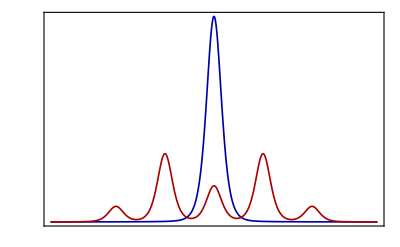

```mathematica
plot2=Plot[{LL,LL1},{a1,-10,10},ImagePadding->70,Axes->False,Frame->{False,False,False,True},FrameTicks->{None,None,None,All},FrameStyle->{Automatic,Automatic,Automatic,Black},ImageSize->Scaled[0.75],FrameLabel->{{None,Style["dI/dV",Small,Bold,Black]},{None,None}},PlotStyle->{{Directive[Darker[Blue]],Thickness[0.003]},{Directive[Darker[Red]],Thickness[0.003]}},PlotRange->Full]
```

```mathematica
Overlay[{plot1,plot2}]
```

-Graphics--Graphics-

```mathematica
Γ=0.05;
ϵ=0;
μ=0;
Subscript[ω, 0]=3;
a=Subscript[Δ, 0]/ω;
L1=(n-m)*Subscript[ω, 0];
β=3.5;
Subscript[D, nm]=Exp[-g^2/2]∑_(o=0)^Min[n,m] (((-1)^o*√(n!*m!)*(g)^(n+m-2*o))/((n-o)!*(m-o)!o!));
f[x_]:=1/2 Γ^2∑_(n=0)^2 ∑_(m=0)^1 (Subscript[D, nm])^2(1/((x-ϵ-L1)^2+Γ^2))(1/(Exp[β(m*Subscript[ω, 0])]+Exp[β((m-1)*Subscript[ω, 0])])+1/(Exp[β(n*Subscript[ω, 0])]+Exp[β((n-1)*Subscript[ω, 0])]+Exp[β((n-2)*Subscript[ω, 0])]))(-(1+Exp[β(x+μ+a1)])^-1+(1+Exp[β(x+μ-a1)])^-1)
f1[x_]:=Γ^2/1 1/((x-ϵ)^2+Γ^2)(-(1+Exp[β(x+μ+a1)])^-1+(1+Exp[β(x+μ-a1)])^-1)
P[x_]:=1/2 Γ^2∑_(n=0)^2 ∑_(m=0)^1 (Subscript[D, nm])^2(1/((x-ϵ-L1)^2+Γ^2))(1/(Exp[β(m*Subscript[ω, 0])]+Exp[β((m-1)*Subscript[ω, 0])])+1/(Exp[β(n*Subscript[ω, 0])]+Exp[β((n-1)*Subscript[ω, 0])]+Exp[β((n-2)*Subscript[ω, 0])]))((Exp[β(x+μ+a1)](1+Exp[β(x+μ+a1)])^-2+Exp[β(x+μ-a1)](1+Exp[β(x+μ-a1)])^-2))
P1[x_]:=Γ^2/1 1/((x-ϵ)^2+Γ^2)((Exp[β(x+μ+a1)](1+Exp[β(x+μ+a1)])^-2+Exp[β(x+μ-a1)](1+Exp[β(x+μ-a1)])^-2))

Subscript[X, I]=-30;
Subscript[X, F]=30;
l=1000;
H=(Subscript[X, F]-Subscript[X, I])/l;
x=Subscript[X, I];
A=∑_(k=1)^l f[x+k*H];
A1=∑_(k=1)^l f1[x+k*H];
B=∑_(k=1)^l P[x+k*H];
B1=∑_(k=1)^l P1[x+k*H];
Fi=(H/2*(f[-30]+f[30]+2*A));
Fi1=(H/2*(f1[-30]+f1[30]+2*A1));
Gi=(H/2*(P[-30]+P[30]+2*B));
Gi1=(H/2*(P1[-30]+P1[30]+2*B1));
```

```mathematica
g=0.5;
LL1=Fi;
LL3=Fi1;
```

```mathematica
g=1;
LL2=Fi;
```

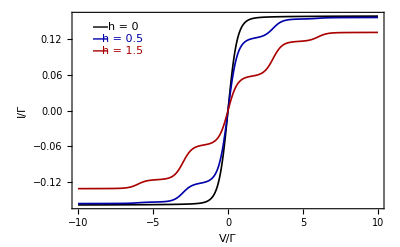

```mathematica
plot1=Plot[{LL3,LL1,LL2},{a1,-10,10},ImagePadding->70,Frame->{True,True,True,False},FrameStyle->{Automatic,Black,Automatic,Automatic},ImageSize->Scaled[0.75],FrameLabel->{{Style["I/Γ ",Small,Bold,Black],None},{Style["V/Γ " ,Small,Bold,Black],None}},PlotStyle->{{Directive[Darker[Black]],Thickness[0.003]},{Directive[Darker[Blue]],Thickness[0.003]},{Directive[Darker[Red]],Thickness[0.003]}}, Epilog->{Darker[Black],Line[{{-9,.14},{-8,.14}}],Text[" h = 0",{-7,.14}],Darker[Blue],Line[{{-8,.12},{-9,.12}}],Text[" h = 0.5",{-7,.12}],Darker[Red],Line[{{-9,.10},{-8,.10}}],Text[" h = 1.5",{-7,.10}]
},PlotRange->Full]
```

```mathematica
g=0.5;
LL1=Gi;
LL3=Gi1;
```

```mathematica
g=1;
LL2=Gi;
```

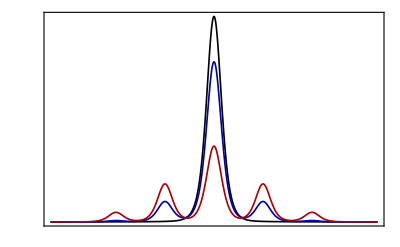

```mathematica
plot2=Plot[{LL3,LL1,LL2},{a1,-10,10},ImagePadding->70,Axes->False,Frame->{False,False,False,True},FrameTicks->{None,None,None,All},FrameStyle->{Automatic,Automatic,Automatic,Black},ImageSize->Scaled[0.75],FrameLabel->{{None,Style["dI/dV",Small,Bold,Black]},{None,None}},PlotStyle->{{Directive[Darker[Black]],Thickness[0.003]},{Directive[Darker[Blue]],Thickness[0.003]},{Directive[Darker[Red]],Thickness[0.003]}}, PlotRange->Full]
```

```mathematica
Overlay[{plot1,plot2}]
```

-Graphics--Graphics-